```mathematica
x={0.831,.84087,.8751,.8775,.879,.82533}
```

{0.831,0.84087,0.8751,0.8775,0.879,0.82533}

```mathematica
xerror={.007,.00026,.0061,.051,.005,.019}
```

{0.007,0.00026,0.0061,0.051,0.005,0.019}

```mathematica
{0.007,0.00026,0.0061,0.051,0.005,0.0}
```

```mathematica
plotxvalues=Table[Around[x[[i]],xerror[[i]]],{i,1,Length[x]}]
```

{0.8310.007,0.840870.00026,0.8750.006,0.880.05,0.8790.005,0.8250.019}

```mathematica
y={1,2,3,4,5,6}
```

{1,2,3,4,5,6}

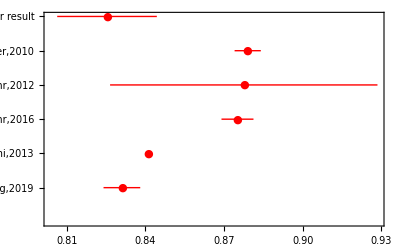

```mathematica
b=ListPlot[Transpose[{plotxvalues,y}],PlotStyle->Red,PlotMarkers->{"●"}, Frame->True, Joined->{False, True},FrameTicks->{Automatic,{{1,"Xiong,2019"},{2,"Antognini,2013"},{3,"Mohr,2016"},{4,"Mohr,2012"},{5,"Bernauer,2010"},{6,"Our result"}}}]
```

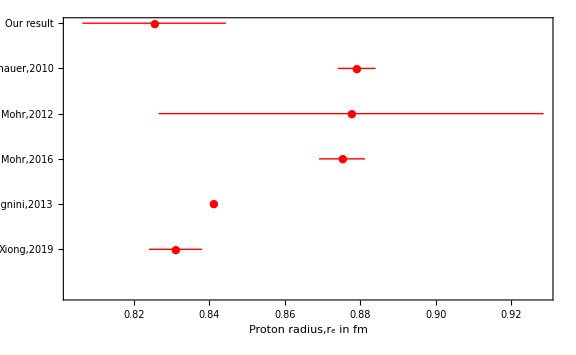

```mathematica
Show[b,ImageSize->Large,FrameLabel->"Proton radius,r_e in fm"]
```

```mathematica
Show[%27,ImageSize->Large]
```

-Graphics-

```mathematica
Show[%28,PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

-Graphics-

```mathematica
l=1
```

1

```mathematica
m=.82533
```

0.82533

```mathematica
merror=.002
```

0.002

```mathematica
plotmvalues=Around[m[[i]],merror[[i]]],{i,1,Length[m]}
```